```mathematica
SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

Global`

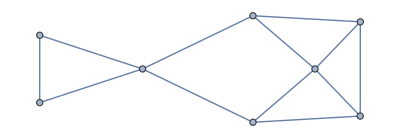
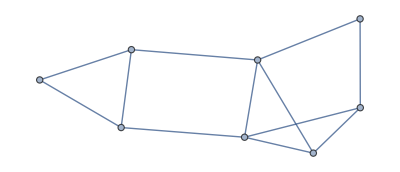
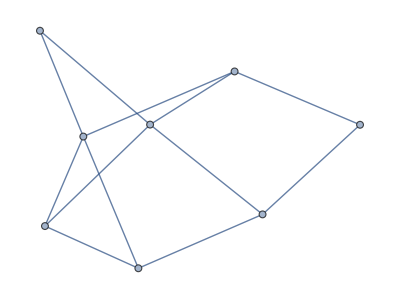

```mathematica
System`RandomGraph[DegreeGraphDistribution[{3,4,2,3,3,4,2,3}],3]
```

```mathematica
(*Neighbors[i_,j_, m_,n_,dist_] := Select[Complement[Flatten[Table[{i+di, i+dj},{di,-dist,dist},{dj,-dist,dist}],1],{{i,j}}],
1<=First[#]<=5 && 1≤Last[#]≤4 &]*)
```

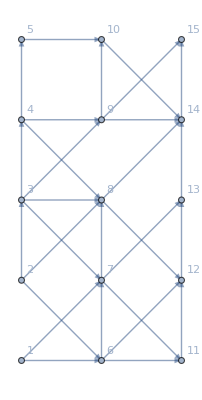

{1<->7,1<->6,2<->3,2<->6,3<->4,3<->9,4<->8,5<->10,5<->4,6<->7,7<->8,7<->11,7<->3,8<->3,8<->2,9<->14,9<->4,9<->15,10<->14,10<->9,11<->12,11<->6,12<->13,12<->6,12<->8,13<->7,13<->14,14<->8,14<->15}

```mathematica
RandomGrid1[m_,n_,maxDist_:1, maxDegree_:4]:= Module[{elist={},
vlist = Range[1,m*n],
vcoords= Flatten[Table[{i,j},{i,1,m},{j,1,n}],1]},

Vertex1D[ij_] := (First[ij]-1)*n+Last[ij];
Neighbors[i_,j_,dist_] := Select[Flatten[Table[{i+di, j+dj},{di,-dist,dist},{dj,-dist,dist}],1],
1<=First[#]≤m && 1≤Last[#]≤n && #≠{i,j}&];
elist={};
Do[With[{newE = {Vertex1D[{i,j}],Vertex1D[adj]}},
AppendTo[elist,newE]],{i,1,m},{j,1,n},{adj, RandomChoice[Neighbors[i,j,maxDist],maxDegree]}]
elist =DeleteDuplicates[elist,#1==#2||#1==Reverse[#2]& ];
newG=System`Graph[vlist,elist,VertexCoordinates->vcoords,
System`VertexWeight->Table[1/Length[vlist], Length[vlist]],System`EdgeWeight-> Table[1,Length[elist]],
System`VertexLabels->Automatic,
System`EdgeStyle->Directive[Opacity[0.5], Thick], EdgeShapeFunction->"Arrow"];
newG (*UndirectedGraph[newG]*)]
(*m=4;
n=4;
maxDist = 1;
maxDegree = 2;
*)

g=RandomGrid1[3,5]
EdgeList[g]
```

```mathematica
RandomGrid2[m_,n_,maxDist_:1]:= Module[{newE},
g= System`GridGraph[{m,n},System`EdgeStyle->Directive[Dashed,Thick]
(*, EdgeShapeFunction->"Arrow"*)];
VertexDistance[i_,j_] :=
With[{x1=Mod[i-1,m], x2=Mod[j-1,m],y1=Quotient[i-1,m],y2=Quotient[j-1,m]},((x1-x2)^2+(y1-y2)^2)^(1/2)];
newE = Flatten[Table[UndirectedEdge[i,j],{i,1,m*n-1},
{j, RandomChoice[
Select[Range[i+1,m*n],0<VertexDistance[i,#,m,n]≤maxDist^2&]
,RandomInteger[{0,2}]]}],1];
g=Graph[System`EdgeAdd[g,newE],System`VertexWeight->Table[1/Length[m*n], Length[m*n]],System`EdgeWeight-> Automatic]]

g= RandomGrid2[3,3]
```

-Graphics-

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

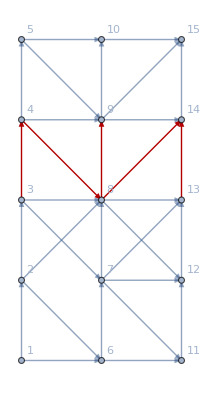

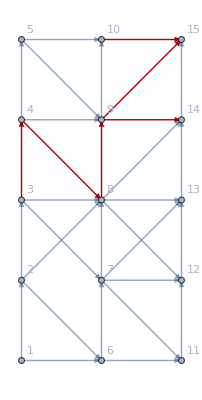

{6.21725×10^-16,0.629833,1.42434,2.15506,2.38373}

-Graphics-

```mathematica
(*GG = System`GridGraph[{3,4}, VertexLabels->Automatic,VertexWeight->Table[1/12,12]]*)
(*ShowSpectralCut[newG]*)
ShowSpectralCut[g]
ShowIsoperimetricCut[g]
ShowMultipleFiedlerCut[g]
```

```mathematica
Plot performances on GridGraphs
```

Range::range: Range specification in Range[1,n^2] does not have appropriate bounds.

Table::iterb: Iterator {i,1,n} does not have appropriate bounds.

Do::iterb: Iterator {i,1,n} does not have appropriate bounds.

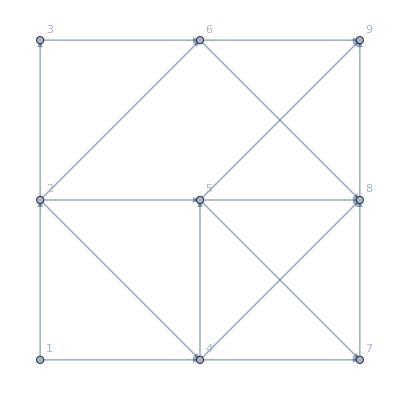

```mathematica
RandomGrid[n_] = RandomGrid1[n,n];

RandomGrid1[3,3]
```

```mathematica
SquareGrid[n_] := System`GridGraph[{n,n}, 
VertexLabels->If[n<10,Automatic,None],VertexWeight->Table[1/n/n,n*n], EdgeWeight->Automatic];
graphs = Map[RandomGrid1[#,#,  max]&, Range[3,18,3]];

SpectralMetrics = Map[EvaluatePartitionAlg[SpectralAlg, #]&, graphs];
SpectralTimes = Transpose[SpectralMetrics][[1]]
SpectralObjs = Transpose[SpectralMetrics][[2]]
IsoperimetricMetrics = Map[EvaluatePartitionAlg[IsoperimetricAlg, #]&, graphs];
IsoperimetricTimes = Transpose[IsoperimetricMetrics][[1]]
IsoperimetricObjs = Transpose[IsoperimetricMetrics][[2]]
MultipleFiedlerMetrics = Map[EvaluatePartitionAlg[MultipleFiedlerAlg, #]&, graphs];
MultipleFiedlerTimes = Transpose[MultipleFiedlerMetrics][[1]]
MultipleFiedlerObjs = Transpose[MultipleFiedlerMetrics][[2]]
```

Eigensystem::arh: Because finding 144 out of the 144 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

Eigensystem::arh: Because finding 225 out of the 225 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

Eigensystem::arh: Because finding 324 out of the 324 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

General::stop: Further output of Eigensystem::arh will be suppressed during this calculation.

{0.,0.03125,0.171875,0.28125,0.546875,1.01563}

{45/2,144/5,5103/88,19440/299,455625/4897,33696/323}

{0.,0.015625,0.078125,0.234375,0.53125,0.96875}

{45/2,144/5,39366/649,23328/299,50625/472,368/3}

{1.77636×10^-15,1.61,2.19171,3.,3.90427}

{-6.5534×10^-17,0.271507,0.395013,0.735666,1.02019}

{-4.11194×10^-17,0.192566,0.208289,0.369166,0.727968}

{2.31296×10^-18,0.0998107,0.108068,0.195329,0.377432}

{2.51651×10^-17,0.0677633,0.0782836,0.140501,0.273707}

{6.16791×10^-18,0.0467401,0.0482243,0.0953544,0.187719}

{0.,0.03125,0.140625,0.671875,2.1875,2.03125}

{45/2,3888/155,6561/110,207360/2783,46575/464,7128/65}

```mathematica
EvaluatePartitionAlg[SpectralAlg, RandomGrid1[3,4]]
```

{0.015625,20,{2<->3,3<->6,7<->6,7<->10,10<->11}}

```mathematica
graphs = Map[SquareGrid[#]&, Range[10,50,5]];
EvaluatePartitionAlg[SpectralAlg, graphs[[3]]]
```

EvaluatePartitionAlg[SpectralAlg,SquareGrid[20]]

```mathematica
MultipleFiedlerObjs
```

{27/2,27,81/2,54,135/2,1994544/24563}

{Spectral,Isoperimetric,MultipleFiedler}

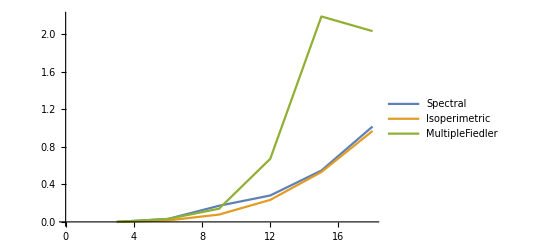

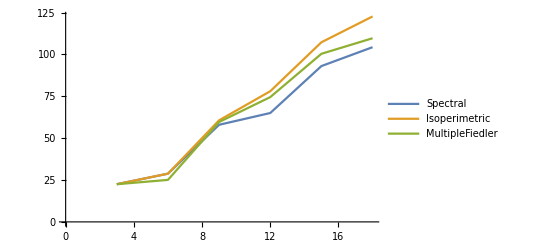

```mathematica
legends = {"Spectral","Isoperimetric","MultipleFiedler"}
ListLinePlot[{SpectralTimes, IsoperimetricTimes, MultipleFiedlerTimes},PlotLegends->legends, DataRange->{3,18}]
ListLinePlot[{SpectralObjs, IsoperimetricObjs, MultipleFiedlerObjs}, PlotLegends->legends, DataRange->{3,18}]
```

```mathematica
NewMultipleFiedlerMetrics = Map[EvaluatePartitionAlg[MultipleFiedlerAlg , #]&, graphs];
NewMultipleFiedlerTimes = Transpose[NewMultipleFiedlerMetrics][[1]]
NewMultipleFiedlerObjs = Transpose[NewMultipleFiedlerMetrics][[2]]
```

{1.77636×10^-17,0.381964,0.38197,0.763929,1.38175}

{-9.28077×10^-17,0.152238,0.152244,0.304484,0.585771}

{-9.1754×10^-17,0.0810139,0.0810141,0.162028,0.31749}

{-6.11756×10^-17,0.0501441,0.0501442,0.100288,0.198062}

{-9.94975×10^-17,0.0340538,0.0340538,0.0681076,0.135056}

{-1.00475×10^-16,0.0246233,0.0246233,0.0492466,0.0978869}

{0.015625,0.109375,0.28125,0.671875,1.23438,2.3125}

{125/6,512/15,1331/28,2744/45,4913/66,8000/91}

{Spectral,Isoperimetric,MultipleFiedler,NewMultipleFiedler}

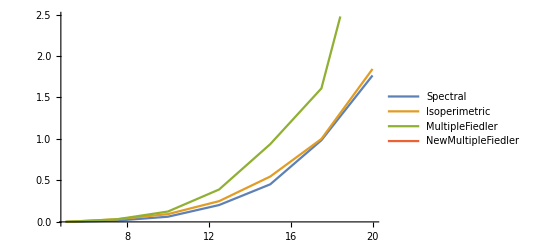

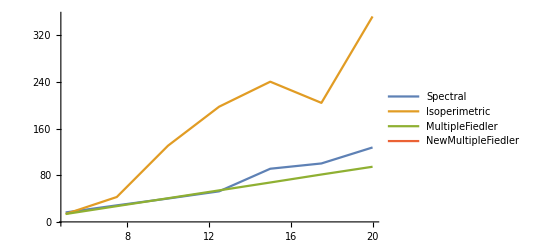

```mathematica
legends = {"Spectral","Isoperimetric","MultipleFiedler","NewMultipleFiedler"}
ListLinePlot[{SpectralTimes, IsoperimetricTimes, MultipleFiedlerTimes,NewMultipleFiedlerTimes},PlotLegends->legends, DataRange->{5,20}]
ListLinePlot[{SpectralObjs, IsoperimetricObjs, MultipleFiedlerObjs,NewMultipleFiedlerObjs}, PlotLegends->legends, DataRange->{5,20}]
```

```mathematica
{1,2,3,4,5}[[-1]]
```

5

```mathematica
SpectralVectors[graphs[[1]],5]
```

{1.77636×10^-17,0.381964,0.38197,0.763929,1.38175}

{{-0.265609,-0.0120993,-0.44704,-0.361697,-0.128612},{-0.265609,0.0755792,-0.363936,-0.223601,-0.145496},{-0.265609,0.217458,-0.22955,-7.86807×10^-6,-0.156061},{-0.265609,0.359344,-0.0951482,0.223594,-0.145592},{-0.265609,0.44703,-0.0121099,0.36182,-0.128651},{-0.265609,-0.0951662,-0.359344,-0.223559,0.0660551},{-0.265609,-0.00749663,-0.276278,-0.138209,0.0491295},{-0.265609,0.1344,-0.141856,-0.0000226543,0.0386194},{-0.265609,0.276274,-0.00746622,0.138165,0.0491373},{-0.265609,0.363945,0.0755675,0.223577,0.0661443},{-0.265609,-0.229565,-0.217462,-3.72085×10^-6,0.186364},{-0.265609,-0.141866,-0.134389,6.79419×10^-6,0.169368},{-0.265609,-9.03508×10^-6,-1.0098×10^-6,-0.0000323116,0.158943},{-0.265609,0.141868,0.13439,-0.0000235516,0.169468},{-0.265609,0.229548,0.217451,-0.0000305295,0.186506},{-0.265609,-0.363952,-0.0755764,0.223582,0.0660945},{-0.265609,-0.276275,0.00748512,0.13816,0.0491426},{-0.265609,-0.134397,0.141885,-0.0000261074,0.0386537},{-0.265609,0.0074835,0.276288,-0.138205,0.0491497},{-0.265609,0.0951461,0.359324,-0.223619,0.0661493},{-0.265609,-0.447005,0.0121007,0.361797,-0.128564},{-0.265609,-0.359319,0.0951708,0.223604,-0.145539},{-0.265609,-0.217455,0.229555,6.74538×10^-6,-0.156047},{-0.265609,-0.0755819,0.363942,-0.223564,-0.145623},{-0.265609,0.0121116,0.446998,-0.36171,-0.128737}}

```mathematica
MatrixForm[%2347]
```

(-0.396604 | -0.255864 | -0.095385
0.641719 | 0.489664 | 0.249721
1.94612×10^-9 | -0.244864 | -0.308672
-0.641719 | -0.0934666 | 0.249721
0.396604 | 0.10453 | -0.095385
0.641719 | 0.594195 | 0.249721
-1.03832 | -1.08386 | -0.653779
3.90971×10^-9 | 0.396198 | 0.808115
1.03832 | 0.442798 | -0.653779
-0.641719 | -0.349331 | 0.249721
-2.98037×10^-10 | -0.583131 | -0.308672
9.14449×10^-10 | 0.943526 | 0.808115
2.34312×10^-9 | 1.69717×10^-14 | -0.998885
-8.23357×10^-10 | -0.943526 | 0.808115
1.00615×10^-9 | 0.583131 | -0.308672
-0.641719 | 0.349331 | 0.249721
1.03832 | -0.442798 | -0.653779
-2.78603×10^-10 | -0.396198 | 0.808115
-1.03832 | 1.08386 | -0.653779
0.641719 | -0.594195 | 0.249721
0.396604 | -0.10453 | -0.095385
-0.641719 | 0.0934666 | 0.249721
4.85575×10^-10 | 0.244864 | -0.308672
0.641719 | -0.489664 | 0.249721
-0.396604 | 0.255864 | -0.095385)

```mathematica
MatrixForm[%2345]
```

(0.552016 | -1.0226 | 0.0387266 | 0.947214 | -0.768015 | 0.2514 | -0.98315 | 0.377403 | 0.173222 | -0.496374 | -0.576806 | 0.192749 | 0.651653 | -0.113544 | -0.219596 | 0.41484 | -0.435212 | -0.0173658 | -2.11177×10^-16 | 0.196568 | -0.11714 | -0.213287 | -0.00139509 | 0.12078 | -0.0236068
0.552016 | -0.834698 | -0.163969 | 0.58541 | -0.411043 | -0.452999 | -0.304747 | -0.447029 | 0.596234 | 0.380139 | 0.22032 | 0.632196 | -0.541326 | -0.305393 | 0.38306 | -0.606199 | 0.267063 | -0.339797 | 0.411516 | -0.425818 | -0.0440589 | 0.345106 | -0.0574353 | -0.256514 | 0.0618034
0.552016 | -0.530664 | -0.491937 | -1.03548×10^-15 | -0.190422 | -0.888341 | 0.374372 | -0.840868 | 0.334798 | -0.161576 | 0.712971 | -2.93755×10^-15 | -2.44547×10^-15 | 0.00502466 | -0.592057 | 0.309157 | 0.264894 | 0.74661 | 0.0208009 | 0.458501 | 0.322398 | -3.73752×10^-15 | 0.193169 | 0.197684 | -0.0763932
0.552016 | -0.22663 | -0.819906 | -0.58541 | -0.411043 | -0.452999 | 0.536121 | -0.0726565 | 0.0733627 | -0.703291 | 0.22032 | -0.632196 | 0.541326 | -0.305393 | 0.38306 | -0.490916 | -0.46384 | -0.102625 | -0.506881 | -0.425818 | -0.0440589 | -0.345106 | -0.255119 | -0.063345 | 0.0618034
0.552016 | -0.0387266 | -1.0226 | -0.947214 | -0.768015 | 0.2514 | 0.377403 | 0.98315 | 0.496374 | 0.173222 | -0.576806 | -0.192749 | -0.651653 | -0.113544 | -0.219596 | 0.373118 | 0.367096 | -0.286822 | 0.0745642 | 0.196568 | -0.11714 | 0.213287 | 0.12078 | 0.00139509 | -0.0236068
0.552016 | -0.819906 | 0.22663 | 0.58541 | -0.0636169 | 0.608372 | 0.0726565 | 0.536121 | -0.703291 | -0.0733627 | 0.22032 | -0.824944 | -0.110327 | 0.489112 | -0.027747 | -0.223481 | 0.603362 | 0.374528 | -0.411516 | -0.163885 | 0.39548 | 0.345106 | 0.063345 | -0.255119 | 0.0618034
0.552016 | -0.632002 | 0.0239343 | 0.361803 | 0.293356 | -0.0960262 | 0.23209 | -0.0890928 | -0.280279 | 0.80315 | -0.0841549 | -0.192749 | -0.651653 | 0.297263 | 0.574909 | -0.117798 | -0.0967441 | -0.389448 | -0.432317 | 0.196568 | -0.11714 | -0.558394 | -0.0059097 | 0.511633 | -0.161803
0.552016 | -0.327968 | -0.304034 | 4.3599×10^-16 | 0.513977 | -0.531368 | 0.231375 | -0.519685 | -0.541715 | 0.261435 | -0.272331 | 2.7437×10^-15 | 3.38489×10^-15 | 0.607681 | -0.400209 | 0.787957 | -0.0681162 | -0.304188 | 0.0745642 | -0.0653659 | -0.556679 | -2.4417×10^-15 | -0.312554 | -0.319859 | 0.2
0.552016 | -0.0239343 | -0.632002 | -0.361803 | 0.293356 | -0.0960262 | -0.0890928 | -0.23209 | -0.80315 | -0.280279 | -0.0841549 | 0.192749 | 0.651653 | 0.297263 | 0.574909 | -0.191359 | -0.16815 | -0.357163 | 0.411516 | 0.196568 | -0.11714 | 0.558394 | 0.511633 | 0.0059097 | -0.161803
0.552016 | 0.163969 | -0.834698 | -0.58541 | -0.0636169 | 0.608372 | -0.447029 | 0.304747 | -0.380139 | 0.596234 | 0.22032 | 0.824944 | 0.110327 | 0.489112 | -0.027747 | -0.25532 | -0.270352 | 0.67627 | 0.357753 | -0.163885 | 0.39548 | -0.345106 | -0.256514 | 0.0574353 | 0.0618034
0.552016 | -0.491937 | 0.530664 | -1.18989×10^-15 | 0.371725 | 0.828994 | 0.840868 | 0.374372 | -0.161576 | -0.334798 | 0.712971 | -2.13233×10^-15 | -2.92264×10^-15 | -0.486006 | -0.338165 | -0.073561 | -0.0714057 | 0.0322851 | 0.843833 | -0.0653659 | -0.556679 | -3.38411×10^-15 | -0.197684 | 0.193169 | -0.0763932
0.552016 | -0.304034 | 0.327968 | 4.3599×10^-16 | 0.728698 | 0.124595 | 0.519685 | 0.231375 | 0.261435 | 0.541715 | -0.272331 | -3.57874×10^-16 | 3.534×10^-15 | -0.677855 | 0.264491 | 0.041722 | -0.802309 | 0.269457 | -0.0745642 | 0.458501 | 0.322398 | -2.7844×10^-15 | 0.319859 | -0.312554 | 0.2
0.552016 | 7.46623×10^-17 | 0. | 1.88929×10^-15 | 0.949319 | -0.310747 | -1.2088×10^-15 | -4.02932×10^-16 | 2.85491×10^-15 | 3.59967×10^-15 | -0.881281 | 1.37185×10^-15 | -1.3122×10^-15 | -0.367437 | -0.710626 | -1.39905×10^-15 | 3.6428×10^-15 | 2.56052×10^-15 | -1.30666×10^-15 | -0.786271 | 0.468561 | 1.12233×10^-14 | -1.30515×10^-16 | 1.18279×10^-15 | -0.247214
0.552016 | 0.304034 | -0.327968 | 9.44646×10^-16 | 0.728698 | 0.124595 | -0.519685 | -0.231375 | -0.261435 | -0.541715 | -0.272331 | 8.35039×10^-16 | -2.59459×10^-15 | -0.677855 | 0.264491 | -0.041722 | 0.802309 | -0.269457 | 0.0745642 | 0.458501 | 0.322398 | -3.5983×10^-15 | -0.319859 | 0.312554 | 0.2
0.552016 | 0.491937 | -0.530664 | 2.36161×10^-16 | 0.371725 | 0.828994 | -0.840868 | -0.374372 | 0.161576 | 0.334798 | 0.712971 | -2.72879×10^-15 | -8.94685×10^-17 | -0.486006 | -0.338165 | 0.073561 | 0.0714057 | -0.0322851 | -0.843833 | -0.0653659 | -0.556679 | -2.9022×10^-15 | 0.197684 | -0.193169 | -0.0763932
0.552016 | -0.163969 | 0.834698 | -0.58541 | -0.0636169 | 0.608372 | 0.447029 | -0.304747 | 0.380139 | -0.596234 | 0.22032 | 0.824944 | 0.110327 | 0.489112 | -0.027747 | 0.25532 | 0.270352 | -0.67627 | -0.357753 | -0.163885 | 0.39548 | -0.345106 | 0.256514 | -0.0574353 | 0.0618034
0.552016 | 0.0239343 | 0.632002 | -0.361803 | 0.293356 | -0.0960262 | 0.0890928 | 0.23209 | 0.80315 | 0.280279 | -0.0841549 | 0.192749 | 0.651653 | 0.297263 | 0.574909 | 0.191359 | 0.16815 | 0.357163 | -0.411516 | 0.196568 | -0.11714 | 0.558394 | -0.511633 | -0.0059097 | -0.161803
0.552016 | 0.327968 | 0.304034 | 9.44646×10^-16 | 0.513977 | -0.531368 | -0.231375 | 0.519685 | 0.541715 | -0.261435 | -0.272331 | -8.35039×10^-16 | -2.59459×10^-15 | 0.607681 | -0.400209 | -0.787957 | 0.0681162 | 0.304188 | -0.0745642 | -0.0653659 | -0.556679 | -2.74156×10^-15 | 0.312554 | 0.319859 | 0.2
0.552016 | 0.632002 | -0.0239343 | 0.361803 | 0.293356 | -0.0960262 | -0.23209 | 0.0890928 | 0.280279 | -0.80315 | -0.0841549 | -0.192749 | -0.651653 | 0.297263 | 0.574909 | 0.117798 | 0.0967441 | 0.389448 | 0.432317 | 0.196568 | -0.11714 | -0.558394 | 0.0059097 | -0.511633 | -0.161803
0.552016 | 0.819906 | -0.22663 | 0.58541 | -0.0636169 | 0.608372 | -0.0726565 | -0.536121 | 0.703291 | 0.0733627 | 0.22032 | -0.824944 | -0.110327 | 0.489112 | -0.027747 | 0.223481 | -0.603362 | -0.374528 | 0.411516 | -0.163885 | 0.39548 | 0.345106 | -0.063345 | 0.255119 | 0.0618034
0.552016 | 0.0387266 | 1.0226 | -0.947214 | -0.768015 | 0.2514 | -0.377403 | -0.98315 | -0.496374 | -0.173222 | -0.576806 | -0.192749 | -0.651653 | -0.113544 | -0.219596 | -0.373118 | -0.367096 | 0.286822 | -0.0745642 | 0.196568 | -0.11714 | 0.213287 | -0.12078 | -0.00139509 | -0.0236068
0.552016 | 0.22663 | 0.819906 | -0.58541 | -0.411043 | -0.452999 | -0.536121 | 0.0726565 | -0.0733627 | 0.703291 | 0.22032 | -0.632196 | 0.541326 | -0.305393 | 0.38306 | 0.490916 | 0.46384 | 0.102625 | 0.506881 | -0.425818 | -0.0440589 | -0.345106 | 0.255119 | 0.063345 | 0.0618034
0.552016 | 0.530664 | 0.491937 | 3.63325×10^-16 | -0.190422 | -0.888341 | -0.374372 | 0.840868 | -0.334798 | 0.161576 | 0.712971 | -2.80335×10^-15 | -5.36811×10^-16 | 0.00502466 | -0.592057 | -0.309157 | -0.264894 | -0.74661 | -0.0208009 | 0.458501 | 0.322398 | -2.82724×10^-15 | -0.193169 | -0.197684 | -0.0763932
0.552016 | 0.834698 | 0.163969 | 0.58541 | -0.411043 | -0.452999 | 0.304747 | 0.447029 | -0.596234 | -0.380139 | 0.22032 | 0.632196 | -0.541326 | -0.305393 | 0.38306 | 0.606199 | -0.267063 | 0.339797 | -0.411516 | -0.425818 | -0.0440589 | 0.345106 | 0.0574353 | 0.256514 | 0.0618034
0.552016 | 1.0226 | -0.0387266 | 0.947214 | -0.768015 | 0.2514 | 0.98315 | -0.377403 | -0.173222 | 0.496374 | -0.576806 | 0.192749 | 0.651653 | -0.113544 | -0.219596 | -0.41484 | 0.435212 | 0.0173658 | 0. | 0.196568 | -0.11714 | -0.213287 | 0.00139509 | -0.12078 | -0.0236068)

```mathematica
MatrixForm[%2343]
```

(0.552016 | -1.0226 | 0.0387266 | 0.947214 | -0.768015 | 0.2514 | -0.98315 | 0.377403 | 0.173222 | -0.496374 | -0.576806 | 0.192749 | 0.651653 | -0.113544 | -0.219596 | 0.41484 | -0.435212 | -0.0173658 | -2.11177×10^-16 | 0.196568 | -0.11714 | -0.213287 | -0.00139509 | 0.12078 | -0.0236068
0.552016 | -0.834698 | -0.163969 | 0.58541 | -0.411043 | -0.452999 | -0.304747 | -0.447029 | 0.596234 | 0.380139 | 0.22032 | 0.632196 | -0.541326 | -0.305393 | 0.38306 | -0.606199 | 0.267063 | -0.339797 | 0.411516 | -0.425818 | -0.0440589 | 0.345106 | -0.0574353 | -0.256514 | 0.0618034
0.552016 | -0.530664 | -0.491937 | -1.03548×10^-15 | -0.190422 | -0.888341 | 0.374372 | -0.840868 | 0.334798 | -0.161576 | 0.712971 | -2.93755×10^-15 | -2.44547×10^-15 | 0.00502466 | -0.592057 | 0.309157 | 0.264894 | 0.74661 | 0.0208009 | 0.458501 | 0.322398 | -3.73752×10^-15 | 0.193169 | 0.197684 | -0.0763932
0.552016 | -0.22663 | -0.819906 | -0.58541 | -0.411043 | -0.452999 | 0.536121 | -0.0726565 | 0.0733627 | -0.703291 | 0.22032 | -0.632196 | 0.541326 | -0.305393 | 0.38306 | -0.490916 | -0.46384 | -0.102625 | -0.506881 | -0.425818 | -0.0440589 | -0.345106 | -0.255119 | -0.063345 | 0.0618034
0.552016 | -0.0387266 | -1.0226 | -0.947214 | -0.768015 | 0.2514 | 0.377403 | 0.98315 | 0.496374 | 0.173222 | -0.576806 | -0.192749 | -0.651653 | -0.113544 | -0.219596 | 0.373118 | 0.367096 | -0.286822 | 0.0745642 | 0.196568 | -0.11714 | 0.213287 | 0.12078 | 0.00139509 | -0.0236068
0.552016 | -0.819906 | 0.22663 | 0.58541 | -0.0636169 | 0.608372 | 0.0726565 | 0.536121 | -0.703291 | -0.0733627 | 0.22032 | -0.824944 | -0.110327 | 0.489112 | -0.027747 | -0.223481 | 0.603362 | 0.374528 | -0.411516 | -0.163885 | 0.39548 | 0.345106 | 0.063345 | -0.255119 | 0.0618034
0.552016 | -0.632002 | 0.0239343 | 0.361803 | 0.293356 | -0.0960262 | 0.23209 | -0.0890928 | -0.280279 | 0.80315 | -0.0841549 | -0.192749 | -0.651653 | 0.297263 | 0.574909 | -0.117798 | -0.0967441 | -0.389448 | -0.432317 | 0.196568 | -0.11714 | -0.558394 | -0.0059097 | 0.511633 | -0.161803
0.552016 | -0.327968 | -0.304034 | 4.3599×10^-16 | 0.513977 | -0.531368 | 0.231375 | -0.519685 | -0.541715 | 0.261435 | -0.272331 | 2.7437×10^-15 | 3.38489×10^-15 | 0.607681 | -0.400209 | 0.787957 | -0.0681162 | -0.304188 | 0.0745642 | -0.0653659 | -0.556679 | -2.4417×10^-15 | -0.312554 | -0.319859 | 0.2
0.552016 | -0.0239343 | -0.632002 | -0.361803 | 0.293356 | -0.0960262 | -0.0890928 | -0.23209 | -0.80315 | -0.280279 | -0.0841549 | 0.192749 | 0.651653 | 0.297263 | 0.574909 | -0.191359 | -0.16815 | -0.357163 | 0.411516 | 0.196568 | -0.11714 | 0.558394 | 0.511633 | 0.0059097 | -0.161803
0.552016 | 0.163969 | -0.834698 | -0.58541 | -0.0636169 | 0.608372 | -0.447029 | 0.304747 | -0.380139 | 0.596234 | 0.22032 | 0.824944 | 0.110327 | 0.489112 | -0.027747 | -0.25532 | -0.270352 | 0.67627 | 0.357753 | -0.163885 | 0.39548 | -0.345106 | -0.256514 | 0.0574353 | 0.0618034
0.552016 | -0.491937 | 0.530664 | -1.18989×10^-15 | 0.371725 | 0.828994 | 0.840868 | 0.374372 | -0.161576 | -0.334798 | 0.712971 | -2.13233×10^-15 | -2.92264×10^-15 | -0.486006 | -0.338165 | -0.073561 | -0.0714057 | 0.0322851 | 0.843833 | -0.0653659 | -0.556679 | -3.38411×10^-15 | -0.197684 | 0.193169 | -0.0763932
0.552016 | -0.304034 | 0.327968 | 4.3599×10^-16 | 0.728698 | 0.124595 | 0.519685 | 0.231375 | 0.261435 | 0.541715 | -0.272331 | -3.57874×10^-16 | 3.534×10^-15 | -0.677855 | 0.264491 | 0.041722 | -0.802309 | 0.269457 | -0.0745642 | 0.458501 | 0.322398 | -2.7844×10^-15 | 0.319859 | -0.312554 | 0.2
0.552016 | 7.46623×10^-17 | 0. | 1.88929×10^-15 | 0.949319 | -0.310747 | -1.2088×10^-15 | -4.02932×10^-16 | 2.85491×10^-15 | 3.59967×10^-15 | -0.881281 | 1.37185×10^-15 | -1.3122×10^-15 | -0.367437 | -0.710626 | -1.39905×10^-15 | 3.6428×10^-15 | 2.56052×10^-15 | -1.30666×10^-15 | -0.786271 | 0.468561 | 1.12233×10^-14 | -1.30515×10^-16 | 1.18279×10^-15 | -0.247214
0.552016 | 0.304034 | -0.327968 | 9.44646×10^-16 | 0.728698 | 0.124595 | -0.519685 | -0.231375 | -0.261435 | -0.541715 | -0.272331 | 8.35039×10^-16 | -2.59459×10^-15 | -0.677855 | 0.264491 | -0.041722 | 0.802309 | -0.269457 | 0.0745642 | 0.458501 | 0.322398 | -3.5983×10^-15 | -0.319859 | 0.312554 | 0.2
0.552016 | 0.491937 | -0.530664 | 2.36161×10^-16 | 0.371725 | 0.828994 | -0.840868 | -0.374372 | 0.161576 | 0.334798 | 0.712971 | -2.72879×10^-15 | -8.94685×10^-17 | -0.486006 | -0.338165 | 0.073561 | 0.0714057 | -0.0322851 | -0.843833 | -0.0653659 | -0.556679 | -2.9022×10^-15 | 0.197684 | -0.193169 | -0.0763932
0.552016 | -0.163969 | 0.834698 | -0.58541 | -0.0636169 | 0.608372 | 0.447029 | -0.304747 | 0.380139 | -0.596234 | 0.22032 | 0.824944 | 0.110327 | 0.489112 | -0.027747 | 0.25532 | 0.270352 | -0.67627 | -0.357753 | -0.163885 | 0.39548 | -0.345106 | 0.256514 | -0.0574353 | 0.0618034
0.552016 | 0.0239343 | 0.632002 | -0.361803 | 0.293356 | -0.0960262 | 0.0890928 | 0.23209 | 0.80315 | 0.280279 | -0.0841549 | 0.192749 | 0.651653 | 0.297263 | 0.574909 | 0.191359 | 0.16815 | 0.357163 | -0.411516 | 0.196568 | -0.11714 | 0.558394 | -0.511633 | -0.0059097 | -0.161803
0.552016 | 0.327968 | 0.304034 | 9.44646×10^-16 | 0.513977 | -0.531368 | -0.231375 | 0.519685 | 0.541715 | -0.261435 | -0.272331 | -8.35039×10^-16 | -2.59459×10^-15 | 0.607681 | -0.400209 | -0.787957 | 0.0681162 | 0.304188 | -0.0745642 | -0.0653659 | -0.556679 | -2.74156×10^-15 | 0.312554 | 0.319859 | 0.2
0.552016 | 0.632002 | -0.0239343 | 0.361803 | 0.293356 | -0.0960262 | -0.23209 | 0.0890928 | 0.280279 | -0.80315 | -0.0841549 | -0.192749 | -0.651653 | 0.297263 | 0.574909 | 0.117798 | 0.0967441 | 0.389448 | 0.432317 | 0.196568 | -0.11714 | -0.558394 | 0.0059097 | -0.511633 | -0.161803
0.552016 | 0.819906 | -0.22663 | 0.58541 | -0.0636169 | 0.608372 | -0.0726565 | -0.536121 | 0.703291 | 0.0733627 | 0.22032 | -0.824944 | -0.110327 | 0.489112 | -0.027747 | 0.223481 | -0.603362 | -0.374528 | 0.411516 | -0.163885 | 0.39548 | 0.345106 | -0.063345 | 0.255119 | 0.0618034
0.552016 | 0.0387266 | 1.0226 | -0.947214 | -0.768015 | 0.2514 | -0.377403 | -0.98315 | -0.496374 | -0.173222 | -0.576806 | -0.192749 | -0.651653 | -0.113544 | -0.219596 | -0.373118 | -0.367096 | 0.286822 | -0.0745642 | 0.196568 | -0.11714 | 0.213287 | -0.12078 | -0.00139509 | -0.0236068
0.552016 | 0.22663 | 0.819906 | -0.58541 | -0.411043 | -0.452999 | -0.536121 | 0.0726565 | -0.0733627 | 0.703291 | 0.22032 | -0.632196 | 0.541326 | -0.305393 | 0.38306 | 0.490916 | 0.46384 | 0.102625 | 0.506881 | -0.425818 | -0.0440589 | -0.345106 | 0.255119 | 0.063345 | 0.0618034
0.552016 | 0.530664 | 0.491937 | 3.63325×10^-16 | -0.190422 | -0.888341 | -0.374372 | 0.840868 | -0.334798 | 0.161576 | 0.712971 | -2.80335×10^-15 | -5.36811×10^-16 | 0.00502466 | -0.592057 | -0.309157 | -0.264894 | -0.74661 | -0.0208009 | 0.458501 | 0.322398 | -2.82724×10^-15 | -0.193169 | -0.197684 | -0.0763932
0.552016 | 0.834698 | 0.163969 | 0.58541 | -0.411043 | -0.452999 | 0.304747 | 0.447029 | -0.596234 | -0.380139 | 0.22032 | 0.632196 | -0.541326 | -0.305393 | 0.38306 | 0.606199 | -0.267063 | 0.339797 | -0.411516 | -0.425818 | -0.0440589 | 0.345106 | 0.0574353 | 0.256514 | 0.0618034
0.552016 | 1.0226 | -0.0387266 | 0.947214 | -0.768015 | 0.2514 | 0.98315 | -0.377403 | -0.173222 | 0.496374 | -0.576806 | 0.192749 | 0.651653 | -0.113544 | -0.219596 | -0.41484 | 0.435212 | 0.0173658 | 0. | 0.196568 | -0.11714 | -0.213287 | 0.00139509 | -0.12078 | -0.0236068)

```mathematica
MatrixForm[%2341]
```

(-0.396604 | -0.255864 | -0.095385
0.641719 | 0.489664 | 0.249721
1.94612×10^-9 | -0.244864 | -0.308672
-0.641719 | -0.0934666 | 0.249721
0.396604 | 0.10453 | -0.095385
0.641719 | 0.594195 | 0.249721
-1.03832 | -1.08386 | -0.653779
3.90971×10^-9 | 0.396198 | 0.808115
1.03832 | 0.442798 | -0.653779
-0.641719 | -0.349331 | 0.249721
-2.98037×10^-10 | -0.583131 | -0.308672
9.14449×10^-10 | 0.943526 | 0.808115
2.34312×10^-9 | 1.69717×10^-14 | -0.998885
-8.23357×10^-10 | -0.943526 | 0.808115
1.00615×10^-9 | 0.583131 | -0.308672
-0.641719 | 0.349331 | 0.249721
1.03832 | -0.442798 | -0.653779
-2.78603×10^-10 | -0.396198 | 0.808115
-1.03832 | 1.08386 | -0.653779
0.641719 | -0.594195 | 0.249721
0.396604 | -0.10453 | -0.095385
-0.641719 | 0.0934666 | 0.249721
4.85575×10^-10 | 0.244864 | -0.308672
0.641719 | -0.489664 | 0.249721
-0.396604 | 0.255864 | -0.095385)